# δ - interaction

## on 2 particles configuration

From Nuclear Structure from a Simple Prespective, P.114

```mathematica
A[lp_,jp_,ln_,jn_,J_,V1_]:=(2jp+1)(2jn+1)ThreeJSymbol[{jp,0.5},{jn,-0.5},{J,0}]^2((1+(-1)^(lp+lp+J))/2+V1((1-(-1)^(lp+ln+J))/2+If[J==0,0,(((2jp+1)+(-1)^(jp+jn+J)(2jn+1))^2)/(4J(J+1))]))
```

{{6.,0},{3.25714,1},{1.37143,2},{1.82857,3},{0.571429,4},{2.85714,5}}

{{6.,0},{6.51429,1},{1.37143,2},{3.65714,3},{0.571429,4},{5.71429,5}}

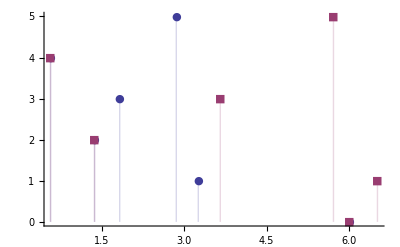

```mathematica
h1=Table[{A[2,5/2,2,5/2,J,1],J},{J,0,5}]
h2=Table[{A[2,5/2,2,5/2,J,2],J},{J,0,5}]
ListPlot[{h1,h2},PlotRange->{{-1,All},{-1,6}},Filling->Axis,PlotMarkers->{Automatic,Large}]
```

{{3.6,1},{1.77143,2},{0.742857,3},{2.57143,4}}

{{7.2,1},{3.2,2},{1.48571,3},{4.,4}}

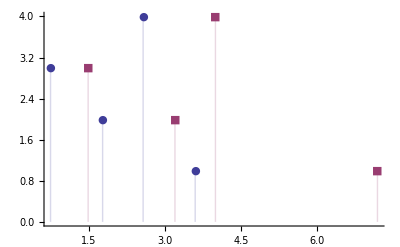

```mathematica
k1=Table[{A[2,5/2,2,3/2,J,1],J},{J,1,4}]
k2=Table[{A[2,5/2,2,3/2,J,2],J},{J,1,4}]
ListPlot[{k1,k2},PlotRange->{{-1,All},{-1,6}},Filling->Axis,PlotMarkers->{Automatic,Large}]
```